```mathematica
vk=0.84; (*конечная скорость*)
 a=0.3; (*ускорение*)
ϵ=10^-10; (*погрешность*)
t0=vk/a; (*время разгона*)
```

```mathematica
s [t_]:=If[t<0,0,If[t<t0,a t^2/2,vk t-a t0^2/2]]; (*координата от времени*)
v[t_]:=If[t<0,0,If[t<t0,a t,vk]]; (*скорость от времени*)
w[t_]:=If[t<0,0,If[t<t0,a,0]]; (*ускорение*)

tzap[x_,y_,t_]:=Module[{t1,t2},
t1=t; t2=t-2ϵ;
While[Abs[t1-t2]>ϵ,t1=t2;t2=t-√((x-s[t1])^2+y^2)]; (*расчет итерациями запаздывающего момента*)
t2
]; (*tzap*)

klw[x_,y_,t_]:=Module[{t2,r,nx,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; k=1-nx v[t2];
k
]; (*k*)

Rlw[x_,y_,t_]:=Module[{t2,r,nx,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; k=1-nx v[t2];
k*r
]; (*Радиус Лиенара Вихерта*)

phi[x_,y_,t_]:=Module[{t2,r,nx,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; k=1-nx v[t2];
1/(k*r)
]; (*phi - скалярный потенциал Лиенара Вихерта*)
electrgradphi[x_,y_,t_]:=Module[{t2,r,nx,ny,n,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; ny=y/r; n={nx,ny};k=1-nx v[t2];
1/(r^2 k^2)((1-v[t2]^2+r nx w[t2])n/k-{v[t2],0})
]; (*эл. поле - grad phi*)

electrgradphiM[x_,y_,t_]:=Module[{ee},
ee=electrgradphi[x,y,t];
√(ee.ee)
]; (*его модуль*)

electrdAdt[x_,y_,t_]:=Module[{t2,r,nx,ny,n,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; ny=y/r; n={nx,ny};k=1-nx v[t2];
1/(r^2 k^2)({v[t2],0}(1/k(v[t2]^2-r nx w[t2]-1)+1)-r{w[t2],0})
]; (*эл. поле dA_dt*)

electrdAdtM[x_,y_,t_]:=Module[{ee},
ee=electrdAdt[x,y,t];
√(ee.ee)
]; (*его модуль*)
electr[x_,y_,t_]:=Module[{t2,r,nx,ny,n,k},
t2=tzap[x,y,t];(*расчет итерациями запаздывающего момента*)
r=t-t2; nx=(x-s[t2])/r; ny=y/r; n={nx,ny};k=1-nx v[t2];
1/k^3((1-v[t2]^2+r nx w[t2])/r^2(n-{v[t2],0})-k/r{w[t2],0})
]; (*эл. поле*)
electrM[x_,y_,t_]:=Module[{ee},
ee=electr[x,y,t];
√(ee.ee)
]; (*его модуль*)

electrMM[x_,y_,t_]:=Module[{ee},
ee=electrgradphi[x,y,t]+electrdAdt[x,y,t];
√(ee.ee)
]; 

electrMPM[x_,y_,t_]:=Module[{ee},
ee=electrgradphi[x,y,t]-electrdAdt[x,y,t];
√(ee.ee)
];
```

```mathematica
t=10;
```

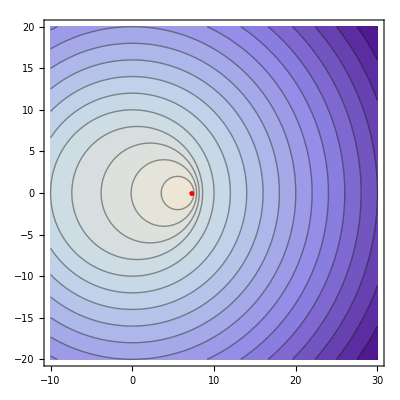

```mathematica
Show[
ContourPlot[tzap[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,-200,200,2}], PlotPoints->30,AspectRatio->Automatic],
Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

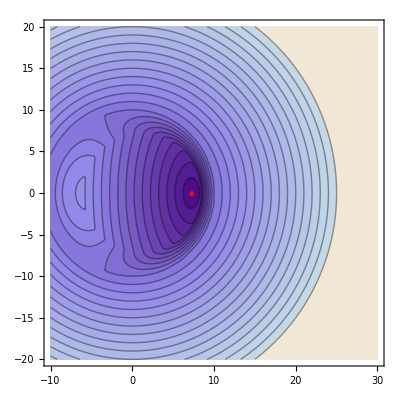

```mathematica
Show[
ContourPlot[Rlw[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,1,25,1}], PlotPoints->30,AspectRatio->Automatic],
Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

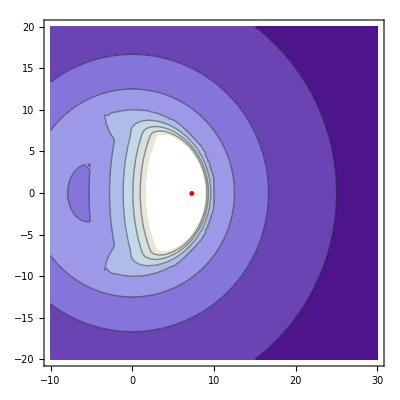

```mathematica
Show[
ContourPlot[phi[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,0.02,1,0.02}], PlotPoints->30,AspectRatio->Automatic],
Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

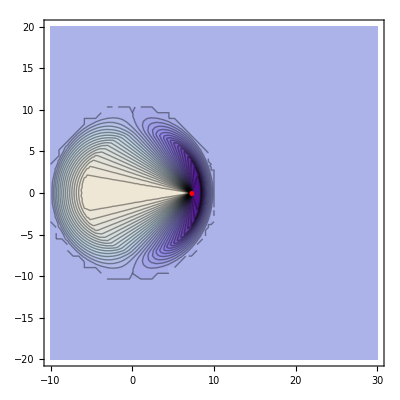

```mathematica
Show[
ContourPlot[klw[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,0.05,5,0.05}], PlotPoints->30,AspectRatio->Automatic],
Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

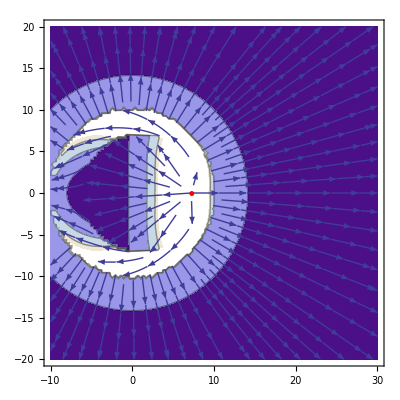

```mathematica
Show[
ContourPlot[electrM[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,0.005,2,0.005}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electr[x,y,t],{x,-10,30},{y,-20,20},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

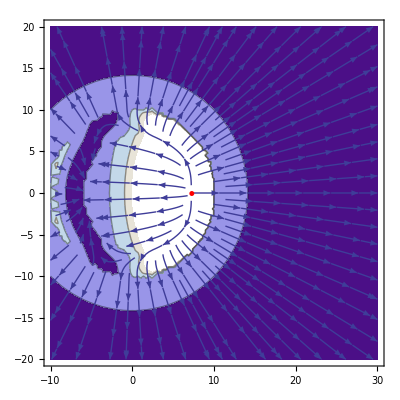

```mathematica
Show[
ContourPlot[electrgradphiM[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,0.005,2,0.005}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electrgradphi[x,y,t],{x,-10,30},{y,-20,20},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

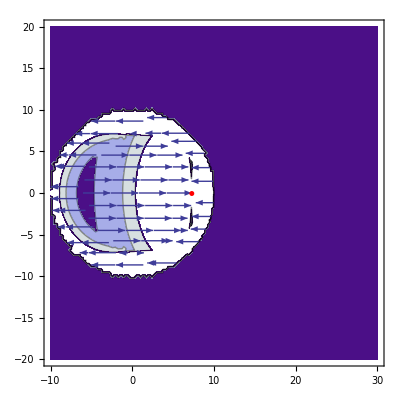

```mathematica
Show[
ContourPlot[electrdAdtM[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,0.005,2,0.005}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electrdAdt[x,y,t],{x,-10,30},{y,-20,20},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

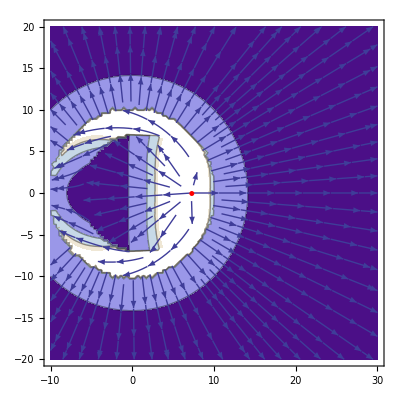

```mathematica
Show[
ContourPlot[electrMM[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,0.005,2,0.005}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electrgradphi[x,y,t]+electrdAdt[x,y,t],{x,-10,30},{y,-20,20},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

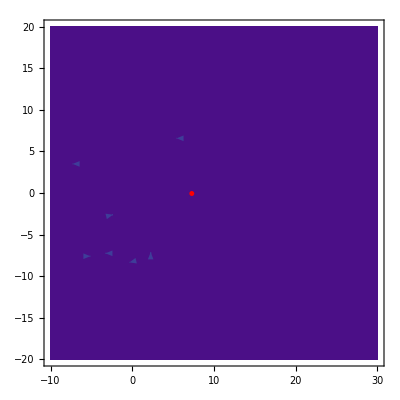

```mathematica
Show[
ContourPlot[electrMM[x,y,t]-electrM[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,0.005,2,0.005}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electrgradphi[x,y,t]+electrdAdt[x,y,t]-electr[x,y,t],{x,-10,30},{y,-20,20},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

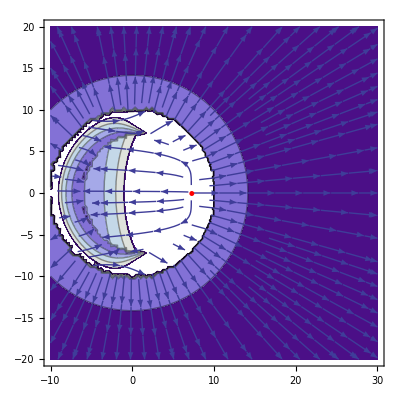

```mathematica
Show[
ContourPlot[electrMPM[x,y,t],{x,-10,30},{y,-20,20},Contours->Table[k,{k,0.005,2,0.005}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electrgradphi[x,y,t]-electrdAdt[x,y,t],{x,-10,30},{y,-20,20},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
]
```

```mathematica
(*ss=Monitor[Table[
Show[
ContourPlot[electrM[x,y,t],{x,-10,30},{y,-10,10},Contours->Table[k,{k,0.005,2,0.005}], PlotPoints->30,AspectRatio->Automatic],
StreamPlot[electr[x,y,t],{x,-10,30},{y,-10,10},AspectRatio->Automatic],Graphics[{Red,Disk[{s[t],0},0.3],Thickness[0.004]}]
],
{t,0,20,0.25}],
t];*)
```

```mathematica
(*Export["D://lw-electr-v=const_not_log.gif",ss]*)
```